```mathematica
ClearAll;
Off[General::munfl];
SetDirectory[NotebookDirectory[]]
```

/home/kirscher/kette_repo/AcoreNteraction/source_mathematica

## Asymptotic boundary conditions

```mathematica
RiccatiBesselJ[z_,l_]:=z SphericalBesselJ[l,z];
RiccatiBesselN[z_,l_]:=z SphericalBesselY[l,z];
```

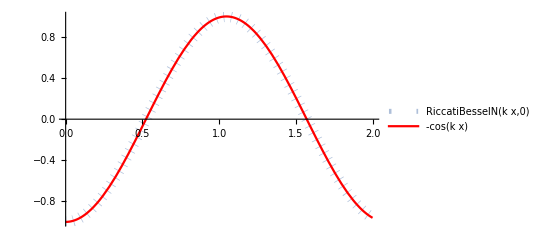

```mathematica
k=3;
Plot[{RiccatiBesselN[k x,0],-Cos[k x]},{x,0,2},PlotLegends->"Expressions",PlotStyle->{{Thickness[0.02],Dotted,Opacity[0.5]},{Red}}]
```

ϕ_k(x)→ u_l(kr)+C v_l(kr)  ⇒  ∂_x ϕ_k(x)=…         u_l=z·j_l , v_l=z·n_l : Riccati-Bessel (Newton)
k=0: ϕ_k(x)→ k^(-l-1)u_l(kr)+C k^l v_l(kr)  ⇒ (ℸ^∼)_l:=h·k^(-l-1)·u_l((∂v_l)/v_l-(∂u_l)/u_l)
(ϕ_k^(n+1)-ϕ_k^n)/h:=(∂v_l)/v_l ϕ_k^n -u_l((∂v_l)/v_l-(∂u_l)/u_l)
α_l:=1+h·(∂v_l)/v_l
β_l:=h·u_l((∂v_l)/v_l-(∂u_l)/u_l)

```mathematica
alpha[r_,k_,l_,h_]:=(1+h (D[FunctionExpand[RiccatiBesselN[k x,l]],x]/.x->r)/(FunctionExpand[RiccatiBesselN[k r,l]]))
beta[r_,k_,l_,h_]:=h FunctionExpand[RiccatiBesselJ[k r,l]](((D[FunctionExpand[RiccatiBesselJ[k x,l]],x])/.x->r)/(FunctionExpand[RiccatiBesselJ[k r,l]])-((D[FunctionExpand[RiccatiBesselN[k x,l]],x])/.x->r)/(FunctionExpand[RiccatiBesselN[k r,l]]))
```

```mathematica
ll=0;
Print["ψ_(N + 1) = α·ψ_N + β"]
Print["L=",ll];
Print["α = ",FullSimplify[alpha["r","p",ll,"h"]],"         lim_(k → 0) =",Simplify[Limit[alpha[h nnGrid,p,ll,"h"],p->0]]];
Print["β = ",FullSimplify[beta["r","p",ll,"h"]],"         lim_(k → 0) =",Limit[beta[h nnGrid,p,ll,"h"]/p^(ll+1),p->0]];
```

ψ_(N + 1) = α·ψ_N + β

L=0

α = 1-h p Tan[p r]         lim_(k → 0) =1

β = h p Sec[p r]         lim_(k → 0) =h

## LECs declaration

LCDa = Johannes parameters
LCDb = E2: -1      MeV    E3: -3       MeV  from PJM paper
LCDc = E2: -2.22 MeV    E3: -8.48  MeV Nuclear case
LCDd = Unitary               E3: -10 MeV

```mathematica
(* Johannes fitting parameters a=12 c.a. *)
LCDa={
{2.,0.00265973,-215.414,0.0},{2.5,0.00265973,-270.193,0.0},{3.,0.00265973,-325.055,0.0},{3.5,0.00265973,-379.981,0.0},{4.,0.00265973,-434.957,0.0},{4.5,0.00265973,-489.974,0.0},{5.,0.00265973,-545.026,0.0},{5.5,0.00265973,-600.107,0.0},{6.,0.00265973,-655.214,0.0},{6.5,0.00265973,-710.343,0.0},{7.,0.00265973,-765.492,0.0},{7.5,0.00265973,-820.659,0.0},{8.,0.00265973,-875.841,0.0},{8.5,0.00265973,-931.039,0.0},{9.,0.00265973,-986.249,0.0},{9.5,0.00265973,-1041.47,0.0},{10.,0.00265973,-1096.71,0.0},{10.5,0.00265973,-1151.95,0.0},{11.,0.00265973,-1207.2,0.0},{11.5,0.00265973,-1262.47,0.0},{12.,0.00265973,-1317.74,0.0},{12.5,0.00265973,-1373.02,0.0},{13.,0.00265973,-1428.3,0.0},{13.5,0.00265973,-1483.6,0.0},{14.,0.00265973,-1538.9,0.0},{14.5,0.00265973,-1594.2,0.0},{15.,0.00265973,-1649.52,0.0},{15.5,0.00265973,-1704.83,0.0},{16.,0.00265973,-1760.16,0.0},{16.5,0.00265973,-1815.49,0.0},{17.,0.00265973,-1870.82,0.0},{17.5,0.00265973,-1926.16,0.0},{18.,0.00265973,-1981.5,0.0},{18.5,0.00265973,-2036.85,0.0},{19.,0.00265973,-2092.2,0.0},{19.5,0.00265973,-2147.55,0.0},{20.,0.00265973,-2202.91,0.0}
};
```

## Solvers

```mathematica
SolveSecularNL0[Rdis_?NumberQ,Npoints_?NumberQ,momentum_?NumberQ,Lin_?NumberQ]:=Block[{p,RRmax,nnGrid,hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,asywf,wf,wffree,tanDelta,fit,nn,δ,L,r,mod,usol,lam,lec},
p=momentum;
RRmax=Rdis;
nnGrid=Npoints;
hDif=RRmax/nnGrid;
L=Lin;

(* Matrix components *)
Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{nnGrid,nnGrid}];
Dmat=DiagonalMatrix[Table[hDif^2 (p^2-mh2 V0[i hDif]-(L(L+1))/(i hDif)^2),{i,1,nnGrid}]];
Wmat=Table[-hDif^3 mh2 W[i hDif,j hDif,p],{i,1,nnGrid},{j,1,nnGrid}]; 

bcol=ConstantArray[0,nnGrid];
ucol=Array[Subscript["u", ##]&,{nnGrid}];
Amat=Dmat+Wmat+Kmat;

If[p==0,
(* ------------------------- zer0 momentum ------------------------- *)

If[L==0,
bcol⟦-1⟧=- hDif;
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+1
,
bcol[[-1]]=1-1./nnGrid;
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+hDif^2 nnGrid;
];

usol=LinearSolve[Amat,bcol];
wf=Table[{i hDif,usol⟦i⟧},{i,1,nnGrid}];

If[L==0,
tanDelta=RRmax-usol⟦-1⟧;
,
tanDelta=RRmax^3/3-usol⟦-1⟧ RRmax;
tanDelta=RRmax-usol⟦-1⟧;
];
,
(* ------------------------- non-zer0 momentum --------------------- *)

(*bcol⟦-1⟧=- hDif p(Cos[p RRmax]+Sin[p RRmax]Tan[p RRmax]);*)
bcol⟦-1⟧=- beta[RRmax,p,L,hDif];
(*Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+1-hDif p Tan[p RRmax];*)
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+alpha[RRmax,p,L,hDif];

usol=LinearSolve[Amat,bcol];

wf=Table[{i hDif,usol⟦i⟧},{i,1,nnGrid}];
tanDelta= (RiccatiBesselJ[p RRmax,L]/RiccatiBesselN[p RRmax,L])-(usol⟦-1⟧/RiccatiBesselN[p RRmax,L]);
];

{tanDelta,wf}
]
```

```mathematica
Scatt1[α0_?NumberQ]:=Block[{f,w},
c0=α0;
(* 1/2 is to have μ instead of m*)
f=Replace[w,NDSolve[{w'[r]+w[r]^2- mh2 Vα0[α0,r]==0,w[0]==10^20},w,{r,0,R}]⟦1,1⟧];R-f[R]^-1]
```

## Solve

```mathematica
(***********************)
(*  Physical quantities   *)
   (***********************)
(*m=1;μ=m/2;hbar=1;mh2=(2 μ)/(hbar)^2;e1=0.1;α=0;
Λl={2.,4.,6.,8.,10.};*)
```

```mathematica
(*
LCDa=Johannes parameters
LCDb=E2:-1 MeV E3:-3 MeV from PJM paper
LCDc=E2:-2.22 MeV E3:-8.48 MeV Nuclear case

anlo(3S1)=5.441 fm = 0.0275735 MeV^-1 anlo(1S0)=-23.748 = -0.120348 MeV^-1
LCDd=Unitary E3:-10 MeV
*)
anpTripl=5.441;
anpSingl=-23.748;
LCD = LCDa;
m=938.92;
μ=m/2;
Lrel=1;
momenta=Range[0.1,8.,1.0];
```

```mathematica
(* Options: *)
Fit2b = False;  (* Do you want to fit the two body lec?*)
aleph = 1/anpTripl;  (* In case to which aleph*)

CalculateFF=True;          (*Calcualte Fermion-Fermion scattering*)
CalculateDD =False;         (*Calcualte Dimer-Dimer scattering*)
CalculateDDstar=False; (*Calculate ab-ac scattering*)
Calculate4H =False;(*Calculate a-abc scattering*)
```

General::munfl: Exp[-710.017] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-711.914] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0241132 (-7.24007×10^-307) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

λ = 8.5         C0 = -931.039

λ = 4.          C0 = -434.957

General::munfl: Exp[-709.09] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-710.889] is too small to represent as a normalized machine number; precision may be lost.

λ = 2.          C0 = -215.414

General::munfl: Exp[-712.69] is too small to represent as a normalized machine number; precision may be lost.

λ = 7.          C0 = -765.492

General::stop: Further output of General::munfl will be suppressed during this calculation.

λ = 5.5         C0 = -600.107

λ = 10.         C0 = -1096.71

λ = 9.          C0 = -986.249

λ = 4.5         C0 = -489.974

λ = 7.5         C0 = -820.659

λ = 2.5         C0 = -270.193

λ = 6.          C0 = -655.214

λ = 10.5        C0 = -1151.95

λ = 5.          C0 = -545.026

General::munfl: Exp[-709.11] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-711.143] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-713.18] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

λ = 9.5         C0 = -1041.47

λ = 8.          C0 = -875.841

General::munfl: Exp[-710.197] is too small to represent as a normalized machine number; precision may be lost.

λ = 6.5         C0 = -710.343

General::munfl: Exp[-712.361] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-709.993] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0241132 (-6.03021×10^-307) is too small to represent as a normalized machine number; precision may be lost.

λ = 3.          C0 = -325.055

General::munfl: Exp[-712.277] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 0.0241132 (-7.31839×10^-307) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-709.69] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-712.089] is too small to represent as a normalized machine number; precision may be lost.

λ = 11.         C0 = -1207.2

General::munfl: Exp[-714.493] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-709.538] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-712.048] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-714.562] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

λ = 14.5        C0 = -1594.2

λ = 13.         C0 = -1428.3

λ = 16.         C0 = -1760.16

λ = 3.5         C0 = -379.981

General::munfl: Exp[-709.02] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-711.634] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-714.252] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

λ = 17.5        C0 = -1926.16

λ = 11.5        C0 = -1262.47

λ = 13.5        C0 = -1483.6

λ = 16.5        C0 = -1815.49

λ = 12.         C0 = -1317.74

λ = 15.         C0 = -1649.52

λ = 18.         C0 = -1981.5

λ = 19.         C0 = -2092.2

λ = 17.         C0 = -1870.82

λ = 14.         C0 = -1538.9

λ = 12.5        C0 = -1373.02

λ = 18.5        C0 = -2036.85

λ = 15.5        C0 = -1704.83

λ = 19.5        C0 = -2147.55

λ = 20.         C0 = -2202.91

-Graphics-

{0.0416919,0.0222384,-0.0295292,0.0385394,0.0331193,0.043714,0.0424594,0.0268707,0.0397651,-0.00685108,0.0353017,0.0442317,0.0303822,0.0431278,0.0408033,0.0370751,0.00687001,0.0446915,0.0468534,0.0461033,0.0474326,0.0159108,0.0478909,0.045102,0.0463764,0.0475969,0.0454705,0.0470625,0.0480228,0.0482608,0.0477493,0.0466255,0.0458026,0.0481458,0.047255,0.0483686,0.0484696}

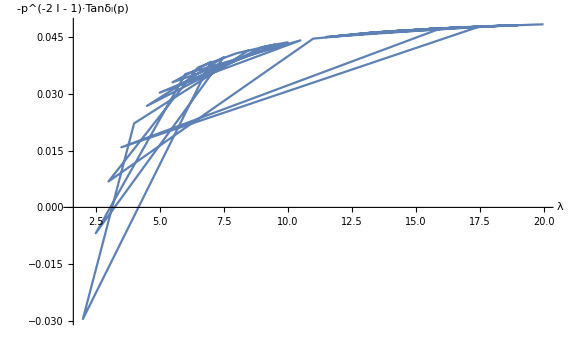

```mathematica
SetSharedVariable[wfkts,tanDeltas,λs,LEC0s,LED0s,αs,ExportData]

Λl=Transpose[LCD]⟦1⟧;
αl=Transpose[LCD]⟦2⟧;
C0l=Transpose[LCD]⟦3⟧;
D0l=Transpose[LCD]⟦4⟧;

LEC0s={};
LED0s={};
αs={};
λs={};
ExportData={};
tanDeltas={};

ParallelDo[{

Λ=Λl⟦j⟧;
λ=N[0.25 Λ^2,3];
λ=Λ;
α=αl⟦j⟧;
C0=C0l⟦j⟧;
D0=D0l⟦j⟧;

AppendTo[LEC0s,     C0];
AppendTo[αs,     α];
AppendTo[λs,    λ];

(* Microscopic calculation: *)
μ1=m/2;hbar=197.327053;mh2=(2 μ1)/(hbar)^2;
V0[r_]                   := C0  Exp[-λ r^2];
Vα0[Cc_,r_]       :=Cc  ⅇ^(-λ r^2);
W[r_,rp_,e_]  :=0;

(*Calculate fermion fermion*)
If[CalculateFF,

nGrid     =800;
R             =9;

tmpsol=SolveSecularNL0[R,nGrid,#,Lrel]&/@momenta;

aleph=aff^-1; (*Scatt1[C0]^-1;*)
α=1.5 aleph^2; (* useless if then you fit the correct dimer-dimer a*)

AppendTo[tanDeltas,  {λ, tmpsol[[All,1]]}];(*tanDeltas[lambda,energy,tanD,wfkt]*)
Print["   λ = "<>StringPadRight[ToString[λ],9]<>"   C0 = "<>StringPadRight[ToString[C0],9]];

];

If[Calculate4H,
(** Trimer - Dimer case^4 H **)
μ1=3/2 μ;hbar=197.327053;mh2=(2 μ1)/(hbar)^2;
nGrid=350;
Rmax=40;

(*D0=0;*)
(* building the interaction is a little long*)

η2=2 C0((3α)/(3α+λ))^(3/2);η3=8D0((3 α^2)/(12 α^2+16α λ+λ^2))^(3/2);
ω2=(3 α λ)/(3α+λ);ω3=(12α λ(α+λ))/(12 α^2+16α λ+λ^2);
ξ1=27/8(3/2 α)^(3/2)mh2^-1;ξ2=-2 27 (3/2 α)^(3/2)C0(α/(4α+λ))^(3/2);ξ3=-27(3/2 α)^(3/2)D0(α/(4α+5 λ))^(3/2);

a1=15/16 α;a2=(3α(5α+8λ))/(4(4α+λ));a3=(3(20 α^2+52α λ+27 λ^2))/(4(16α+20λ));
b1=18/16 α;b2=(9α(α+λ))/(2(4α+λ))λ;b3=(9(4 α^2+8α λ+3 λ^2))/(2(16α+20λ));
c1=15/16 α;c2=(3α(5α+2λ))/(4(4α+λ));c3=(3(20 α^2+28α λ+3 λ^2))/(4(16α+20λ));



V0[r_]:=η2 ⅇ^(-ω2  r^2)+η3 ⅇ^(-ω3  r^2);
W[r_,rp_,p_]:=Re[-(r rp 4 π)(ξ1  ⅇ^(-a1 r^2- c1 rp^2) ((-(4 a1^2 r^2+b1^2 rp^2-2 a1)+2/r^2+p^2) ⅈ SphericalBesselJ[1,ⅈ b1 r rp]+4 a1 b1 r rp (SphericalBesselJ[0,ⅈ b1 r rp]/3
-SphericalBesselJ[2,ⅈ b1 r rp] 2/3))- ξ2 ⅈ SphericalBesselJ[1,ⅈ b2 r rp] ⅇ^(-a2 r^2- c2 rp^2)-ξ3 ⅈ SphericalBesselJ[1,ⅈ b3 r rp] ⅇ^(-a3 r^2- c3 rp^2))];
W[r_,rp_,p_]:=0;

tmpsol=SolveSecularNL0[Rmax,nGrid,#,Lrel]&/@momenta;

AppendTo[tanDeltas,  {λ, tmpsol[[All,1]]}];(*tanDeltas[lambda,energy,tanD,wfkt]*)

AppendTo[ExportData,    {λ,α,C0,D0}];
Print["α = "<>StringPadRight[ToString[α],9]<>"   λ = "<>StringPadRight[ToString[λ],9]<>"   C0 = "<>StringPadRight[ToString[C0],9]<>"   D0 = "<>StringPadRight[ToString[D0],9]];

];


},{j,1,Length[Λl],1}];
(*list=ExportString[ExportData,"Table","FieldSeparators"-> " ", Alignment-> Left];
DeleteFile["./fermion_trimer_parameter.dat"];
WriteString["./fermion_trimer_parameter.dat",list];
Close["./fermion_trimer_parameter.dat"];*)
ListLinePlot[180/Pi ArcTan[tanDeltas[[All,2]]],PlotLabels->λs,AxesLabel->{"p","δ_l(p)"},ImageSize->Large,PlotRange->All]
erepapas=-#[[1]]/momenta[[1]]^(2 Lrel+1)&/@tanDeltas[[All,2]]
ListPlot[Transpose[{tanDeltas[[All,1]],erepapas}],AxesLabel->{"λ","-p^(-2 l - 1)·Tanδ_l(p)"},ImageSize->Large,PlotRange->{All,All},Joined->True]
```

```mathematica
momenta[[1]]
```

0.1

α = 0.0001  λ = 4.

Grid sizes       :{20,30,40,50,60,70,80,90,100,110,120,130,140,150,160,170}

Integration radii:{30,35,40,45,50,55,60,65,70,75,80}

{54.7147,34.1135,19.6165,4.58408,-15.006,-46.5818,-115.471,-439.947,577.634,218.226,147.376,116.454,98.7777,87.1291,78.7392,72.3155}

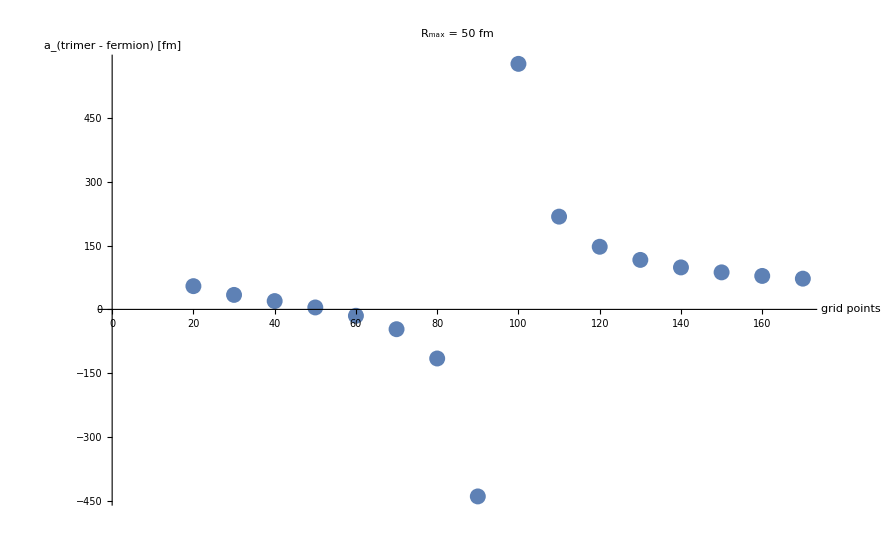

```mathematica
μ1=3/2 μ;hbar=197.327053;mh2=(2 μ1)/(hbar)^2;
nl=22;
Λl=Transpose[LCD]⟦1⟧[[nl]];λ=0.25 Λl^2;
α=0.0001 Transpose[LCD]⟦2⟧[[nl]];
C0=Transpose[LCD]⟦3⟧[[nl]];
D0=Transpose[LCD]⟦4⟧[[nl]];
Print["α = "<>ToString[α]<>"  λ = "<>ToString[λ]]
η2=2 C0((3α)/(3α+λ))^(3/2);η3=8D0((3 α^2)/(12 α^2+16α λ+λ^2))^(3/2);ω2=(3 α λ)/(3α+λ);ω3=(12α λ(α+λ))/(12 α^2+16α λ+λ^2);ξ1=27/8(3/2 α)^(3/2)mh2^-1;ξ2=-2 27 (3/2 α)^(3/2)C0(α/(4α+λ))^(3/2);ξ3=-27(3/2 α)^(3/2)D0(α/(4α+5 λ))^(3/2);
a1=15/16 α;a2=(3α(5α+8λ))/(4(4α+λ));a3=(3(20 α^2+52α λ+27 λ^2))/(4(16α+20λ));b1=18/16 α;b2=(9α(α+λ))/(2(4α+λ))λ;b3=(9(4 α^2+8α λ+3 λ^2))/(2(16α+20λ));c1=15/16 α;c2=(3α(5α+2λ))/(4(4α+λ));c3=(3(20 α^2+28α λ+3 λ^2))/(4(16α+20λ));
V0[r_]:=η2 ⅇ^(-ω2  r^2)+η3 ⅇ^(-ω3  r^2);
W[r_,rp_,p_]:=Re[-(r rp 4 π)(ξ1  ⅇ^(-a1 r^2- c1 rp^2) ((-(4 a1^2 r^2+b1^2 rp^2-2 a1)+2/r^2+p^2) ⅈ SphericalBesselJ[1,ⅈ b1 r rp]+4 a1 b1 r rp (SphericalBesselJ[0,ⅈ b1 r rp]/3
-SphericalBesselJ[2,ⅈ b1 r rp] 2/3))- ξ2 ⅈ SphericalBesselJ[1,ⅈ b2 r rp] ⅇ^(-a2 r^2- c2 rp^2)-ξ3 ⅈ SphericalBesselJ[1,ⅈ b3 r rp] ⅇ^(-a3 r^2- c3 rp^2))];
nGrid=Table[20+10 n,{n,0,15}];
Rmax=Table[30+5 n,{n,0,10}];
Print["Grid sizes       :",nGrid]
Print["Integration radii:",Rmax]

griddy=True;
If[griddy==True,
Rma=50;
aftG=SolveSecularNL0[Rma,#,0.0,1]⟦1⟧&/@nGrid;
Print[aftG];
ListPlot[Transpose[{nGrid,aftG}],AxesLabel->{"grid points","a_(trimer - fermion) [fm]"},PlotLabel->"R_max = "<>ToString[Rma]<>" fm"]
,
aftR=SolveSecularNL0[#,Max[nGrid],0.0,1]⟦1⟧&/@Rmax;
Print[aftR];
ListPlot[Transpose[{Rmax,aftR}],AxesLabel->{"R_max","a_(trimer - fermion) [fm]"}]
]
```

```mathematica
mh2
```

0.0482265

## Result Plot

```mathematica
Print["λ\t\t\tα\t\t\tC0\t D0\t a_ff\t a_(a - abc)"]
For[i=1,i<Length[λs],i++,Print[NumberForm[0.25 Λl⟦i⟧^2,{8,4}],"\t",NumberForm[ αl⟦i⟧,{8,7}],"\t",NumberForm[C0l⟦i⟧,{8,3}],"\t",NumberForm[D0l⟦i⟧,{8,3}],"\t",NumberForm[afts⟦i⟧,{8,2}]]]
```

λ			α			C0	 D0	 a_ff	 a_(a - abc)

0.1000	1	0	0	-343.68

0.1600	1	-5.236	-0.251	-392.47

0.2000	1	-6.212	-0.014	-562.11

0.3000	1	-9.041	0.906	-1207.60

0.3500	1	-10.665	1.563	7367.25

0.4000	1	-12.428	2.365	994.85

0.4500	1	-14.331	3.324	578.80

0.5000	1	-16.373	4.450	436.31

0.5500	1	-18.555	5.754	368.78

0.6000	1	-20.876	7.245	332.07

0.6500	1	-23.336	8.935	310.72

0.7000	1	-25.935	10.834	290.17

0.7500	1	-28.674	12.953	60.08

0.8000	1	-31.552	15.303	194.19

0.8500	1	-34.569	17.894	39.65

0.9000	1	-37.725	20.739	-2.65×10^8

0.9500	1	-41.020	23.847	9.16×10^35

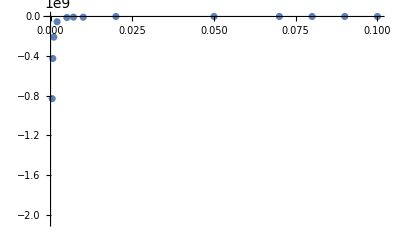

```mathematica
data=Transpose[{Pp,Tp^-1}];
Show[ListPlot[data]]//Print;
```

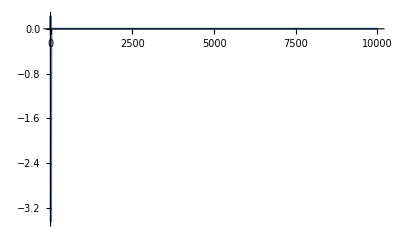

```mathematica
Plot[W[r,r,0.2],{r,0,10000}]
```